Gusarev model of the absorption of the light in the powder bed:

```mathematica
Clear[Pabs,ξ,λ,r,Po];
```

```mathematica
Pabs[ξ_,λ_,r_]:=Po * (r a/((4 r -3)δ)((1-r^2)Exp[-λ] ((1-a)Exp[-2 a ξ]+(1+a)Exp[2a ξ])-(3+r Exp[-2 λ])
((1+a+r(1-a))Exp[2 a (λ-ξ)]+(1-a-r(1+a))Exp[2 a (ξ-λ)]))-(3(1-r)(Exp[-ξ]-r Exp[ξ-2 λ]))/(4 r -3));
```

```mathematica
D[Pabs[ξ,λ,r],ξ]//Simplify
```

1/(-3+4 r)Po (-3 ⅇ^(-2 λ-ξ) (-1+r) (ⅇ^(2 λ)+ⅇ^(2 ξ) r)-(2 ⅇ^(2 (-1+√(1-r)) λ) (1-r) r (-ⅇ^(λ-2 √(1-r) ξ) (-1+ⅇ^(4 √(1-r) ξ) (1+√(1-r))+√(1-r)) (-1+r^2)-ⅇ^(-2 √(1-r) (λ-ξ)) (3 ⅇ^(2 λ)+r) (1-√(1-r)-(1+√(1-r)) r+ⅇ^(4 √(1-r) (λ-ξ)) (-1-√(1-r)+(-1+√(1-r)) r))))/(-2+2 √(1-r)+r+r^2-ⅇ^(4 √(1-r) λ) (-2 (1+√(1-r))+r+r^2)))

```mathematica
Clear[U];
D[Pabs[0,l,ref],ref]
```

3.97887×10^7 ((3 ⅇ^(-2 l) (1-ref))/(-3+4 ref)+(12 (1-ref) (1-ⅇ^(-2 l) ref))/(-3+4 ref)^2+(3 (1-ⅇ^(-2 l) ref))/(-3+4 ref)-1/(-3+4 ref)0.00206987 ref (-ⅇ^(-2 l) (ⅇ^(-1.2 l) (0.4-1.6 ref)+ⅇ^(1.2 l) (1.6+0.4 ref))-4. ⅇ^-l ref-(-1.6 ⅇ^(-1.2 l)+0.4 ⅇ^(1.2 l)) (3+ⅇ^(-2 l) ref))+1/(-3+4 ref)^2 0.00827948 ref (-(ⅇ^(-1.2 l) (0.4-1.6 ref)+ⅇ^(1.2 l) (1.6+0.4 ref)) (3+ⅇ^(-2 l) ref)+2. ⅇ^-l (1-ref^2))-(0.00206987 (-(ⅇ^(-1.2 l) (0.4-1.6 ref)+ⅇ^(1.2 l) (1.6+0.4 ref)) (3+ⅇ^(-2 l) ref)+2. ⅇ^-l (1-ref^2)))/(-3+4 ref))

Global`U

U[l_,ref_]:=∂_ref Pabs[0,l,ref]

the dimensionless depth is ξ=β z and values a and δ are values derived from hemispherical reflectivity r:

```mathematica
a := Sqrt[1-r];
β := 3/(2 d)   ρ/(1-ρ);
λ := β h;
δ :=(1-a)(1-a-r(1+a))Exp[-2 a λ]-(1+a)(1+a-r (1-a))Exp[2 a λ];
```

here ρ is relative powder density, h is powder layer height, d is diameter of particle in powder bed.

```mathematica
r=0.64; ρ = 0.63; d=0.025; h=0.040; ω=0.040;Po=200.0 10^3/(ω^2 π);
```

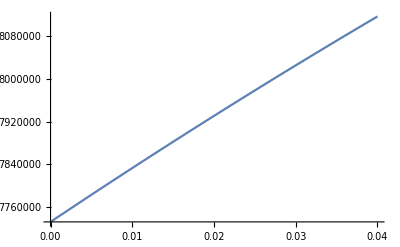

```mathematica
Plot[Pabs[ξ,λ,r], {ξ,0,h}]
```

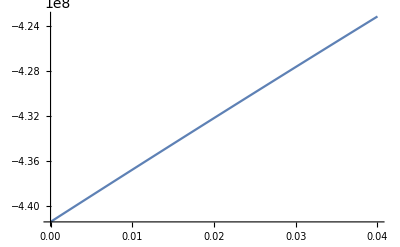

```mathematica
r=0.74;
Plot[Pabs[ξ,λ,r],{ξ,0,h}]
```

Why is the powder density negative for r = 0.74, should be positive ???

```mathematica
Pabs[0,λ,r]
```

-4.41416×10^8

```mathematica
Pabs[ λ 4,λ,r]
```

3.32749×10^11

```mathematica
?a
```

Global`a

a:=√(1-r)

```mathematica
r=0.64;
Pabs[0,λ,r]
```

7.73262×10^6

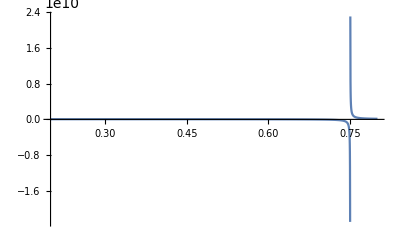

```mathematica
Plot[D[Pabs[0,λ, ref]],{ref,0.2,0.8},PlotRange->All]
```

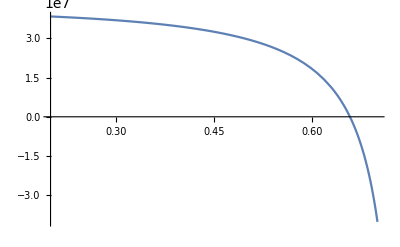

```mathematica
Plot[Pabs[0,λ, ref],{ref,0.2,0.7},PlotRange->All]
```

```mathematica
FindRoot[Pabs[0,λ,ref]==0,{ref,0.2,0.7}]
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

{ref→0.657913}